```mathematica
Integrate[(x1+x2+x3+x4+x5)^3,{x1,0,1},{x2,0,1},{x3,0,1},{x4,0,1},{x5,0,1}]
```

75/4

```mathematica
errorVsN = Import["/home/dk0r/git/comp-phys/HW_2/monteCarlo5Dn.csv"]
```

{{1,1.76275},{2,0.065938},{3,0.353172},{4,0.416917},{5,0.00889227},«49991»,{49997,0.00394344},{49998,0.00183829},{49999,0.00173464},{50000,0.00298005}}

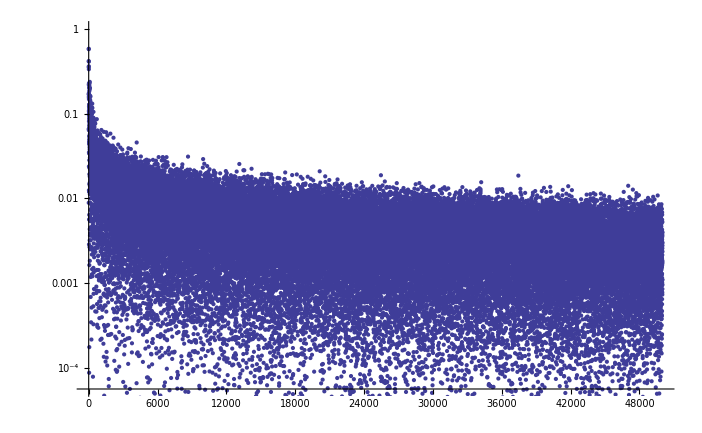

```mathematica
ListLogPlot[errorVsN]
```

```mathematica
newOne = Import["/home/dk0r/git/comp-phys/HW_2/monteCarlo5Dn.csv"]
```

{{N,relError},{1,1.76275},{2,0.065938},{3,0.353172},{4,0.416917},{5,0.00889227},{6,0.582016},{7,0.169638},«49985»,{49993,0.000857737},{49994,0.000968631},{49995,0.00527732},{49996,0.00110403},{49997,0.00394344},{49998,0.00183829},{49999,0.00173464},{50000,0.00298005}}

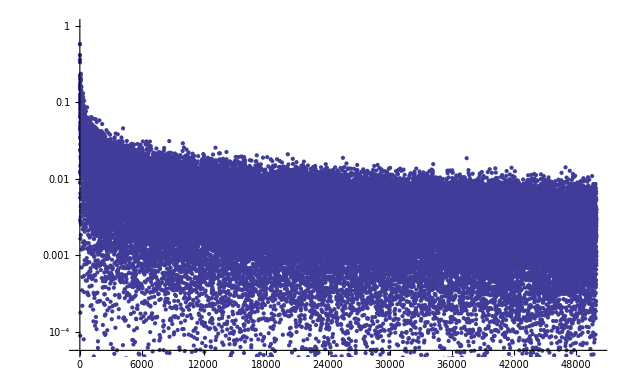

```mathematica
ListLogPlot[newOne]
```

```mathematica
anotherOne = Plot[x^(-1/2),{x,0,50000}]
```

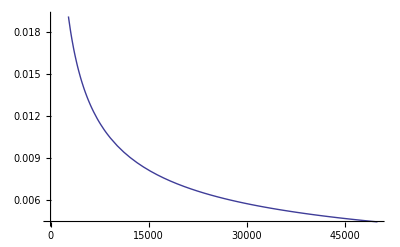

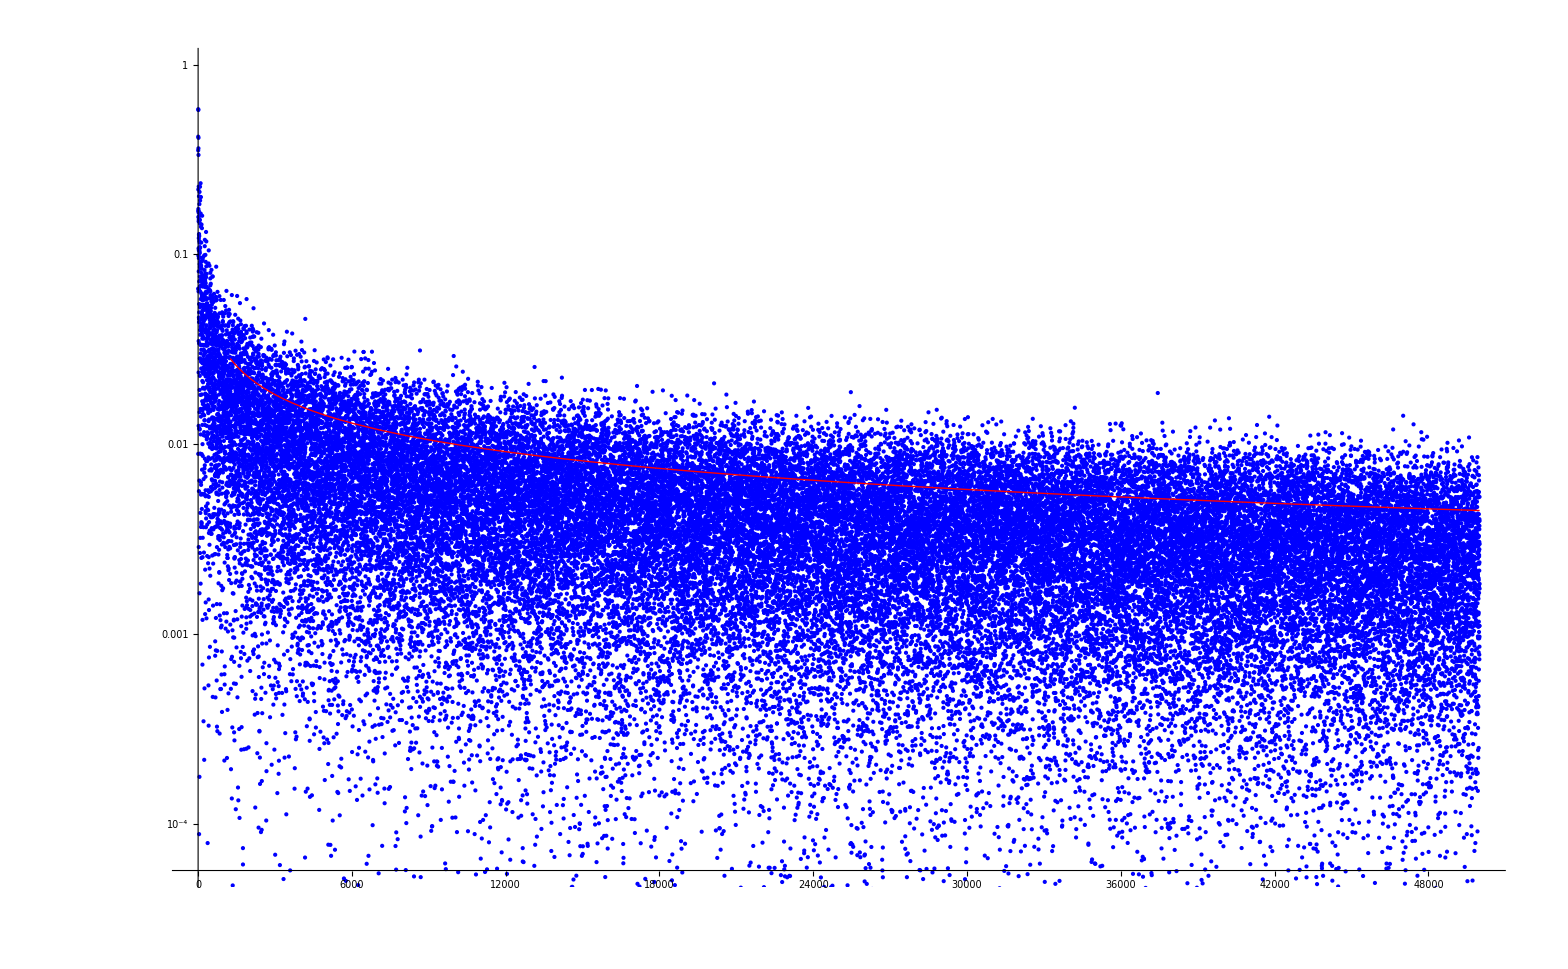

```mathematica
Show[ListLogPlot[newOne, PlotStyle->Blue],LogPlot[x^(-1/2),{x,0,50000}, PlotStyle->Red]]
```

```mathematica
correct = Import["/home/dk0r/git/comp-phys/HW_2/monteCarlo5DnSRAND.csv"]
```

{{N,relError},{1,1.76275},{2,0.065938},{3,0.353172},{4,0.416917},{5,0.00889227},{6,0.582016},{7,0.169638},{8,0.219682},{9,0.576255},{10,0.157408},{11,0.173436},{12,0.0984921},{13,0.361977},{14,0.411164},{15,0.334047},{16,0.0638313},{17,0.107423},«49965»,{49983,0.00193379},{49984,0.000900833},{49985,0.00648016},{49986,0.00426041},{49987,0.000256611},{49988,0.00395561},{49989,0.000347546},{49990,0.00319027},{49991,0.002755},{49992,0.000788048},{49993,0.000687152},{49994,0.00319286},{49995,0.00805535},{49996,0.00491975},{49997,0.00223095},{49998,0.000412431},{49999,0.00417307},{50000,0.0000714062}}

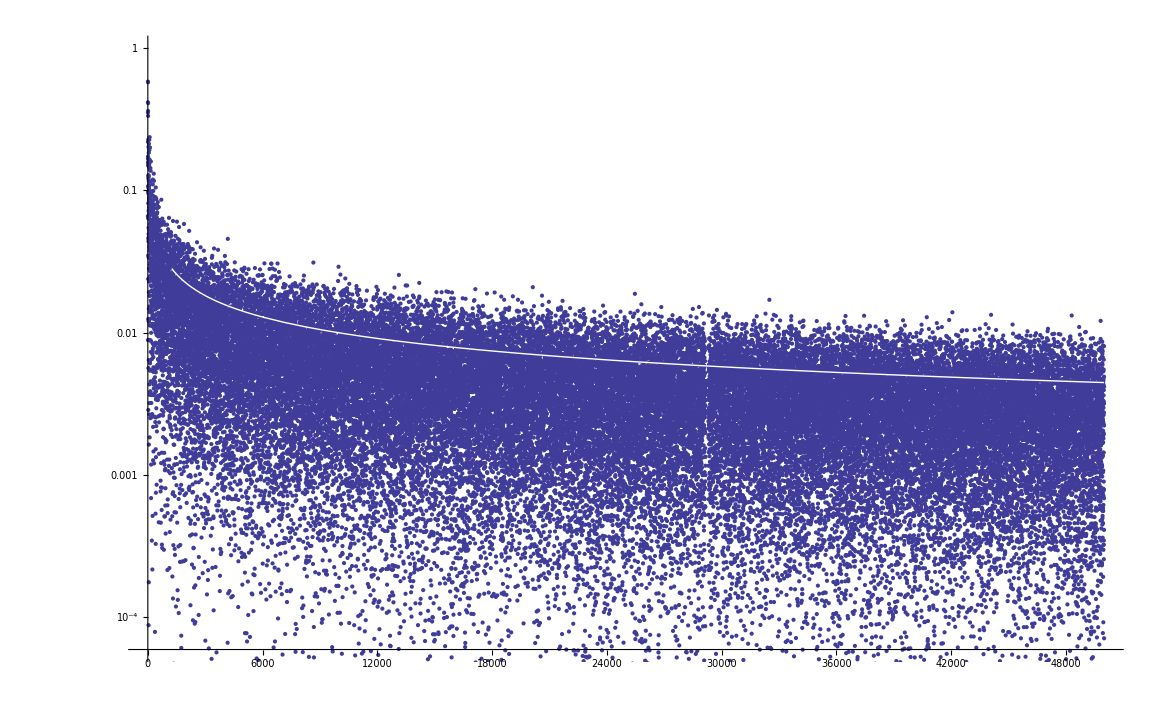

```mathematica
Show[ListLogPlot[correct],LogPlot[x^(-1/2),{x,0,50000}, PlotStyle->White]]
```

```mathematica
sdData = Import["/home/dk0r/git/comp-phys/HW_2/monteCarlo5D.csv"]
```

{{51.8016,17.5137,12.128,26.5672,18.9167,29.6628,15.5693,14.631,29.5548,15.7986,22.0019,16.9033,11.9629,26.4593,25.0134,17.5532,16.7358,15.6342,19.1976,15.9499,18.9843,19.405,14.483,17.2249,18.6962,21.9118,21.0314,15.8798,16.9585,20.718,19.6224,18.856,16.368,14.956,19.5742,19.6067,«49928»,18.7785,18.815,18.8018,18.8704,18.7708,18.7549,18.8296,18.8024,18.7704,18.8338,18.7739,18.7342,18.651,18.7502,18.6692,18.8616,18.9056,18.8616,18.6958,18.6877,18.7043,18.7276,18.7655,18.6905,18.6618,18.7581,18.6366,18.7817,18.7402,18.798,18.757,18.8201,18.6203,18.7658,18.6526,18.7129}}

```mathematica
StandardDeviation[{}]
```